```mathematica
(* 
M= 2;                     (* Defined i *)
Mprime=5;
Ei[i_] := -1/(2*(i+1)^2);             (* Defined E_i *)Constants and Parameters 
T[ω_] := 100; 
Γ23 = Gamma[2/3]; Gamma function *)
Z=1;
a0 = 1;(* 5.29177210544×10^-11;   Bohr radius *)
c=299792458/2.18769126216*10^6; (* Speed of light *)
Ry = 1/2;(*2.1798723611030*10^−18;  Rydberg energy *) 
hbar=1;(* 1.054571817*10^−34;*)
```

```mathematica
g0[n_] :=Sqrt[1/(2*(2n-1)!)] * 4*(4n)^n * Exp[-2n]
```

```mathematica
gup[1][n_, κ_] := Module[{product, Γterm},  (* to be used only for 1s to kp or 2p to kd*)
    product = Product[(1 + s^2 κ^2), {s, 1, n}];
    Γterm = 0;
    If[κ==0,1,Sqrt[product/(1 - Exp[-2π/κ])] * Exp[2n - 2/κ ArcTan[n κ]] * (1 + n^2 κ^2)^(-n-2)] * g0[n]
]
gup[2][n_, κ_] := (1/2) * Sqrt[(2n-1)*(1 + n^2 κ^2)] * gup[1][n, κ]
```

```mathematica
gup[i_][n_,  κ_] /;i>2 := Module[{l,term1, term2, term3},   (* gup[i][n,k]:= g[n,n-i;k,n-i+1] *)
    (* First term *)
  l=n-i+2;
    term1 = (4n^2 - 4l^2 + l(2l-1)(1 + n^2 κ^2)) * gup[i-1][n, κ];
  
    (* Second term *)
    term2 = 2n * Sqrt[(n^2 - l^2)*(1 + (l+1)^2 κ^2)] * gup[i-2][n, κ];
    (* Left side coefficient *)
  
    coeff = 2n*Sqrt[(n^2 - (l-1)^2)*(1 + l^2 κ^2)]; 
    (* Full solution *)
    (term1 - term2)/coeff
]
```

```mathematica
Sigma[n_, l_, W_,lprime_] := Module[{gValue, lmax,w},
    (* Calculate maximum l value *)
    lmax = Max[l, lprime];
    w=(W+Ry/n^2)/hbar;
    (* Calculate the g(n,l;√(2w),l') matrix element - 
       You'll need to implement your g function separately *)
    gValue = gup[n-l][n, Sqrt[W/Ry]]; 
    
    (* Full formula *)
    6*10^-5(4*π^2*w*a0*2*Ry)/(3*c) * (n^4/Z^4)* (lmax/(2*l + 1))  * Abs[gValue]^2
]
```

```mathematica
Print[Sigma[1,0,0,1],Sigma[1,0,0,1]*(5.29177210544×10^−9)^2]
Print[Sigma[5,0,0,1],Sigma[5,0,0,1]*(5.29177210544×10^−9)^2]
Print[Sigma[10,0,0,1],Sigma[10,0,0,1]*(5.29177210544×10^−9)^2]
Print[Sigma[20,0,0,1],Sigma[20,0,0,1]*(5.29177210544×10^−9)^2]
```

6.75394×10^-181.8913×10^-34

5.46356×10^-171.52995×10^-33

1.50054×10^-164.20193×10^-33

4.32007×10^-161.20974×10^-32

```mathematica
kkk=0.01
Print[Sigma[1,0,kkk,1],Sigma[1,0,kkk,1]*(5.29177210544×10^−9)^2]
Print[Sigma[5,0,kkk,1],Sigma[5,0,kkk,1]*(5.29177210544×10^−9)^2]
Print[Sigma[10,0,kkk,1],Sigma[10,0,kkk,1]*(5.29177210544×10^−9)^2]
Print[Sigma[20,0,kkk,1],Sigma[20,0,kkk,1]*(5.29177210544×10^−9)^2]
```

0.01

6.4062×10^-181.79392×10^-34

2.35357×10^-176.59065×10^-34

1.41946×10^-173.9749×10^-34

3.44841×10^-189.65653×10^-35

```mathematica
OmegaW150[W_]:=gup[5][5,Sqrt[2W]](*E0e 5^2/(3Z^2)*)
OmegaW1100[W_]:=gup[10][10,Sqrt[2W]] (*E0e 10^2/(3Z^2)*)
OmegaW1200[W_]:=gup[20][20,Sqrt[2W]](*E0e 20^2/(3Z^2)*)
```

```mathematica
N[OmegaW150[1]]
```

314.393

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

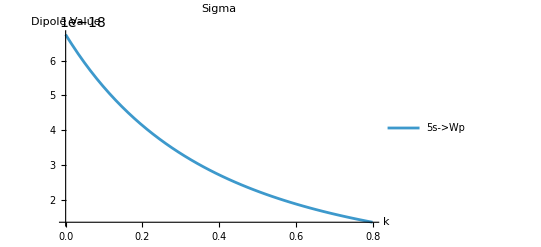

```mathematica
Plot[Evaluate[Sigma[1,0,W/2,1]], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"5s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

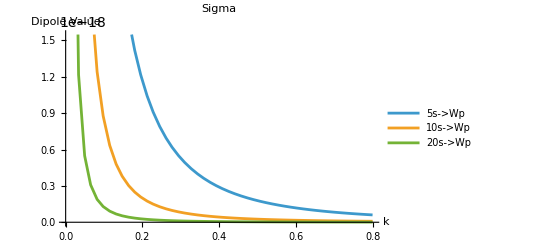

```mathematica
Plot[Evaluate[{Sigma[5,0,W/2,1],Sigma[10,0,W/2,1],Sigma[20,0,W/2,1]}], {W, 0.001, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"5s->Wp","10s->Wp","20s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

General::munfl: Exp[-9829.83] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

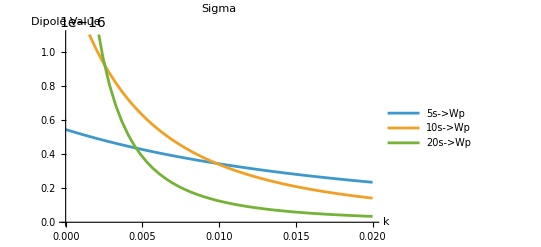

```mathematica
Plot[Evaluate[{Sigma[5,0,W/2,1],Sigma[10,0,W/2,1],Sigma[20,0,W/2,1]}], {W, 0, 0.02},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"5s->Wp","10s->Wp","20s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

```mathematica
OmegaW110[W_]:=E0e /(3Z^2)*g1[1,Sqrt[2W]]
OmegaW120[W_]:=E0e 2^2/(3Z^2)*g2[2,Sqrt[2W]]
OmegaW221[W_]:=E0e 2*2^2/(3Z^2)*g1[2,Sqrt[2W]]
OmegaW021[W_]:=E0e 2^2/(3Z^2)*g3[2,Sqrt[2W]]
```

```mathematica
(* Prefactor term - using En instead of E to avoid conflict *)

(* Sinc-squared term *)
sincTerm[W_, ω_,i_] := Sinc[(W- Ei[i] - ω)/2 * T[ω]]^2



(* Full integrand *)
integrand[W_, ω_,T_] :=  T^2/Mprime* (Abs[OmegaW110[W]]^2sincTerm[W, ω,0]+(Abs[OmegaW120[W]+OmegaW221[W]]^2+Abs[OmegaW021[W]]^2)sincTerm[W,ω,1])



(* Numerical integration for Pni(ω) *)
Pni[ω_?NumericQ, T_?NumericQ] := NIntegrate[integrand[W, ω,T], {W, 0, ∞}]
```

```mathematica
(* Plot range *)
ωmin = 0;
ωmax =- 1.5*Ei[0];
data1 = Table[{ω, Pni[ω,100]}, {ω, ωmin, ωmax, (ωmax - ωmin)/100}]; (* 100 points *)
Export["Pni_data_M=2T=100_v0.wl", data, "WL"];  Wolfram Language format
```

NIntegrate::inumr: The integrand (10000 (Abs[OmegaW110[W]]^2 Sinc[1/2 (W+Times[«2»]) T[0]]^2+(Abs[OmegaW021[W]]^2+Abs[OmegaW120[«1»]+«1»]^2) Sinc[«1»]^2))/Mprime has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

format Language Wolfram

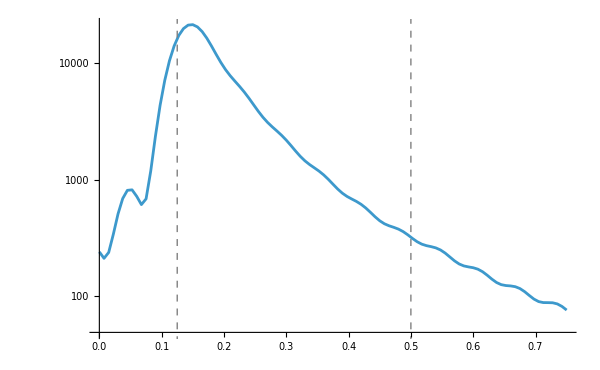
-Graphics-ω (amu)

```mathematica
(* Plot Pni(ω) *)
P = Labeled[
  ListLogPlot[data1, 
 ImageSize -> 600,Joined -> True,
Epilog->Table[{Gray, Dashed, Line[{{1/(2*i^2), 0}, {1/(2*i^2), 40000}}]},{i,M}]],
  Style["ω (amu)",  FontSize -> 20],
  Bottom
]
```

```mathematica
cm = 72/2.54 (* centimetre *)
Export[CloudObject["Exports/IP_M2T=100E0e=1_v0.png"],P, "png",ImageResolution -> 300]
```

28.3465

CloudObject[https://www.wolframcloud.com/obj/vikrantkumar/Exports/IP_M2T=100E0e=1_v0.png]

```mathematica
ωmin = 0;
ωmax =- 1.5*Ei[0];
data2 = Table[{ω, Pni[ω,1000]}, {ω, ωmin, ωmax, (ωmax - ωmin)/100}]; (* 100 points *)
Export["Pni_data_M=2_v0.wl", data2, "WL"]; (* Wolfram Language format *)
```

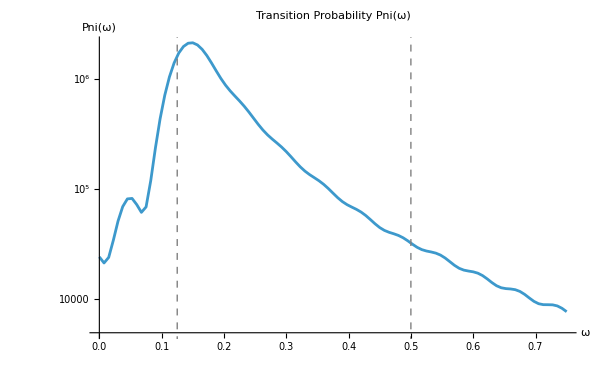

```mathematica
ListLogPlot[data2, 
 PlotLabel -> "Transition Probability Pni(ω)",
 AxesLabel -> {"ω", "Pni(ω)"},
 GridLines -> Automatic,
 ImageSize -> 600,Joined -> True,
Epilog->Table[{Gray, Dashed, Line[{{1/(2*i^2), 0}, {1/(2*i^2), 40000}}]},{i,M}]] (* Control recursion depth *)
```

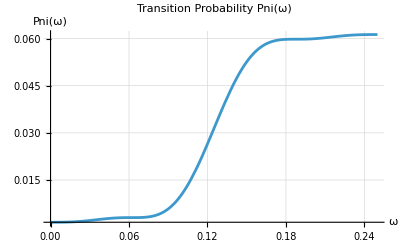

```mathematica
(* Constants and Parameters *)
i = 2;                     (* Defined i *)
Ei =- 1/(2*i^2);             (* Defined E_i *)
Γ23 = Gamma[2/3];          (* Gamma function *)
T[ω_] := 100;             (* T depends on omega *)
E0e = 1;

(* Prefactor term - using En instead of E to avoid conflict *)
prefactor[En_] := 1

(* Sinc-squared term *)
sincTerm[En_, ω_] := Sinc[(En - Ei - ω)/2 * T[ω]]^2

(* Full integrand *)
integrand[En_, ω_] := 1 * prefactor[En] * sincTerm[En, ω]

(* Numerical integration for Pni(ω) *)
Pni[ω_?NumericQ] := NIntegrate[integrand[En, ω], {En, 0, ∞}]

(* Plot range *)
ωmin = 0;
ωmax = -2*Ei;

(* Plot Pni(ω) *)
Plot[Pni[ω], {ω, ωmin, ωmax}, 
 PlotLabel -> "Transition Probability Pni(ω)",
 AxesLabel -> {"ω", "Pni(ω)"},
 PlotRange -> All,
 GridLines -> Automatic,
 PlotPoints -> 30, (* Increase sampling for smoother plot *)
 MaxRecursion -> 3] (* Control recursion depth *)
```